# Temas de Física 4 Cuarta Práctica

Ariadna Uxue Palomino Ylla 20161343

```mathematica
ClearAll["Global`*"]
```

```mathematica
Tabla[F_,a_,b_,p__:0.5]:=Table[F==r,{r,a,b,p}]
```

```mathematica
CN1x1[F_,r_]:=ContourPlot[Evaluate[F[x,y]==r],{x,-9,9},{y,-9,9},ImageSize->{1000,1000},ContourStyle->Directive[White,Thick]];
```

```mathematica
LinCam[f_,g_,n_:4]:=StreamDensityPlot[{f[x,y],g[x,y]},{x,-1*n,n},{y,-1*n,n},ColorFunction->"PearlColors"(*GrayYellowTones*),StreamStyle->RGBColor[0.25,0.84,0.54],StreamPoints->Fine,PerformanceGoal->"Quality",PlotRange->3];(*,StreamScale->Full*)(*Esta función grafica los stramlines*)
```

```mathematica
LinCam3[f_,g_]:=StreamDensityPlot[{f[x,y],g[x,y]},{x,-3,6},{y,-3,6},ColorFunction->"PearlColors"(*GrayYellowTones*),StreamStyle->RGBColor[0.25,0.84,0.54],StreamPoints->Fine,PerformanceGoal->"Quality",PlotRange->3];(*,StreamScale->Full*)(*Esta función grafica los stramlines*)
```

```mathematica
Showing[g1_,g2_,g3___,g4___,g5___]:=Show[{g1,g2,g3,g4,g5},PlotRange->{{-2,2},{-2,2}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
Showing2[g1_,g2_,g3___,g4___,g5___]:=Show[{g1,g2,g3,g4,g5},PlotRange->{{-5,5},{-5,5}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
Showing3[g1_,g2_,g3___,g4___,g5___]:=Show[{g1,g2,g3,g4,g5},PlotRange->{{-3,5},{-2,6}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
Showing4[g1_,g2_,g3___,g4___,g5___]:=Show[{g1,g2,g3,g4,g5},PlotRange->{{-1,3},{-1,5}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
Showing5[g1_,g2_,g3___,g4___,g5___]:=Show[{g1,g2,g3,g4,g5},PlotRange->{{-4,4},{-4,4}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
CurvaNivel[F_,a_,b_,paso_:0.5]:=ContourPlot[Evaluate[Tabla[F[x,y],a,b,paso]],{x,-9,9},{y,-9,9},ImageSize->{1000,1000},ContourStyle->Directive[White,Thick]];
```

```mathematica
Singularidades[f_,g_]:=Solve[{f[x,y]==0,g[x,y]==0},{x,y}]
```

```mathematica
SingularidadesR[f_,g_]:=Solve[{f[x,y]==0,g[x,y]==0},Reals](*Esta función devuelve las singularidades REALES*)
```

```mathematica
Points[f_,g_]:=Graphics[{PointSize[0.015],RGBColor[0.5,0.44,0.84],Point[Table[{x,y}/.Select[Singularidades[f,g],FreeQ[#,Complex]&][[i]],{i,Dimensions[Select[Singularidades[f,g],FreeQ[#,Complex]&]][[1]]}]]}](*Esta función grafica los puntos de las singularidades*)
```

```mathematica
JacMatrix[f_,g_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}//MatrixForm;(*Esta función devuelve la matriz Jacobiana*)
```

```mathematica
Jac[f_,g_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};(*Esta función devuelve lo anterior pero no en forma de matriz*)
```

```mathematica
ode[f_,g_,x0_,y0_,ti_,tf_:10]:=NDSolve[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,ti,tf},MaxSteps->Infinity];(*Esta función produce una sola solución*)
p[f_,g_,x0_,y0_,ti_,tf_:10,color_:Cyan,thicknes_:0.003]:=ParametricPlot[Evaluate[Table[{x[t],y[t]}/.ode[f,g,x0,y0,ti,tf]],{t,ti,tf},PlotStyle->{color,Thickness[thicknes]}, PlotRange->{{-3,3},{-3,3}},PlotPoints->1000,AxesLabel->{"x","y"}]];(*Esta función grafica una solución*)
```

```mathematica
FuncionH[H_]:=Plot3D[H[x,y],{x,-3,3},{y,-3,3},BoxRatios->{1,1,1},ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20},ColorFunction->"NeonColors",AxesLabel->Automatic,PlotLegends->Automatic]
```

```mathematica
CylinderPlot3D[f_,{rMin_,rMax_},{tMin_,tMax_},opts___]:=ParametricPlot3D[{r Cos[t],r Sin[t],f[r,t]},{r,rMin,rMax},{t,tMin,tMax},opts]
```

```mathematica
CylinderParametric3D[f_,r_,{tMin_,tMax_},opts___]:=ParametricPlot3D[{r Cos[t],r Sin[t],f[r,t]},{t,tMin,tMax},opts]
```

```mathematica
ToPolarFunction[field_]:=TransformedField["Cartesian"->"Polar",field,{x,y}->{r,θ}]
```

```mathematica
Donut[r1_,r2_,extra__]:=RegionPlot[ImplicitRegion[r1^2<x^2+y^2<r2^2,{x,y}],extra](*Dominio anular*)
```

## Pregunta 2

En el siguiente sistema ocurre solo una bifurcación en el origen cuando μ=0; analizarlo en forma cualitativa, estableciendo las singularidades, el tipo de bifurcación presente y estructurar el retrato de fase correspondiente:

Sistema:

Piecewise[{{ẋ=, y+μx}, {ẏ=, -x+μy-x^2 y}}]

```mathematica
$Assumptions=μ∈Reals;
```

```mathematica
f2[x_,y_]:=y+μ*x
```

```mathematica
g2[x_,y_]:=-x+μ*y-x^2*y
```

```mathematica
f2[x_,y_,μ_]:=y+μ*x(*doy dos definiciones según el número de parametros*)
```

```mathematica
g2[x_,y_,μ_]:=-x+μ*y-x^2*y (*doy dos definiciones según el número de parametros*)
```

```mathematica
P1=Singularidades[f2,g2]
```

{{x→0,y→0},{x→-(√(1+μ^2))/(√μ),y→√μ √(1+μ^2)},{x→(√(1+μ^2))/(√μ),y→-√μ √(1+μ^2)}}

Matriz Jacobiana:

```mathematica
JM1=JacMatrix[f2,g2]
```

(μ | 1
-1-2 x y | -x^2+μ)

```mathematica
ClearAll[μ]
```

Hay 3 singularidades dependiendo de los valores que tome μ:

❶ Si μ >0 hay 3 singularidades: P1, P2, P3

```mathematica
D1=Normal[Solve[f2[x,y,μ]==0&&g2[x,y,μ]==0&&μ>0,Reals],ConditionalExpression]
```

{{x→0,y→0},{x→-(√(μ+μ^3))/μ,y→√(μ+μ^3)},{x→(√(μ+μ^3))/μ,y→-√(μ+μ^3)}}

Evaluando la matriz Jacobiana en el P1:

```mathematica
JM1/.D1[[1]]
```

(μ | 1
-1 | μ)

Evaluando los autovalores en el P1:

```mathematica
A1[μ_]=Jac[f2,g2]/.D1[[1]]//Eigensystem
```

{{-ⅈ+μ,ⅈ+μ},{{ⅈ,1},{-ⅈ,1}}}

si μ>0 ,{x→0,y→0} corresponde a una singularidad tipo foco espiral inestable

Evaluando la matriz Jacobiana en el P2:

```mathematica
JM1/.D1[[2]]
```

(μ | 1
-1+(2 (μ+μ^3))/μ | μ-(μ+μ^3)/μ^2)

Evaluando los autovalores en el P2:

```mathematica
A2[μ_]=Jac[f2,g2]/.D1[[2]]//Eigensystem
```

{{2 μ,(-1-μ^2)/μ},{{1/μ,1},{-μ/(1+2 μ^2),1}}}

si μ>0, {x→-(√(1+μ^2))/(√μ),y→√μ √(1+μ^2)}  corresponde a una singularidad tipo ensilladura

Evaluando la matriz Jacobiana en el P3:

```mathematica
JM1/.D1[[3]]
```

(μ | 1
-1+(2 (μ+μ^3))/μ | μ-(μ+μ^3)/μ^2)

Evaluando los autovalores en el P3:

```mathematica
A3[μ_]=Jac[f2,g2]/.D1[[3]]//Eigensystem
```

{{2 μ,(-1-μ^2)/μ},{{1/μ,1},{-μ/(1+2 μ^2),1}}}

si μ>0,{x→(√(1+μ^2))/(√μ),y→-√μ √(1+μ^2)}  corresponde a una singularidad tipo ensilladura

❷  Si μ <0 hay 1 singularidad: P1

```mathematica
D2=Normal[Solve[f2[x,y,μ]==0&&g2[x,y,μ]==0&&μ<0,Reals],ConditionalExpression]
```

{{x→0,y→0}}

```mathematica
JM1/.D2[[1]]
```

(μ | 1
-1 | μ)

```mathematica
A4[μ_]=Jac[f2,g2]/.D2[[1]]//Eigensystem
```

{{-ⅈ+μ,ⅈ+μ},{{ⅈ,1},{-ⅈ,1}}}

si μ<0  corresponde a una singularidad tipo foco espiral estable

❸  Si μ =0 hay 1 singularidad: P1

```mathematica
D3=Normal[Solve[f2[x,y,0]==0&&g2[x,y,0]==0,Reals],ConditionalExpression]
```

{{x→0,y→0}}

```mathematica
JM1/.D3[[1]]
```

(μ | 1
-1 | μ)

```mathematica
A5[μ_]=Jac[f2,g2]/.D3[[1]]//Eigensystem
```

{{-ⅈ+μ,ⅈ+μ},{{ⅈ,1},{-ⅈ,1}}}

```mathematica
A5[0]
```

{{-ⅈ,ⅈ},{{ⅈ,1},{-ⅈ,1}}}

si μ=0  corresponde a una singularidad no hiperbolica

Obteniendo el sistema en polares: {ṙ,θ̇}

```mathematica
ClearAll[μ]
```

```mathematica
fr2[r_,θ_]=Replace[
Solve[{x*f2[x,y]+y*g2[x,y]==r*fr2,r^2*fθ2==x*g2[x,y]-y*f2[x,y]},{fr2,fθ2}][[1]][[1]][[2]],{x->r*Cos[θ],y->r*Sin[θ]},{-1}]//FullSimplify(*ṙ*)
```

1/8 r (-r^2+8 μ+r^2 Cos[4 θ])

```mathematica
fθ2[r_,θ_]=Replace[Solve[{x*f2[x,y]+y*g2[x,y]==r*fr2,r^2*fθ2==x*g2[x,y]-y*f2[x,y]},{fr2,fθ2}][[1]][[2]][[2]],{x->r*Cos[θ],y->r*Sin[θ]},{-1}]//FullSimplify(*θ̇*)
```

-1-r^2 Cos[θ]^3 Sin[θ]

Sistema
ṙ=1/8 r (-r^2+8 μ+r^2 Cos[4 θ])
θ̇=-1-r^2 Cos[θ]^3 Sin[θ]

```mathematica
U1[r_,θ_]=Solve[fr2[r,θ]==0,{μ}](*ṙ=0*)
```

{{μ→1/8 (r^2-r^2 Cos[4 θ])}}

```mathematica
fu[r_,θ_]=U1[r,θ][[1]][[1]][[2]]//Simplify(*μ=1/8 (r^2-r^2 Cos[4 θ])*)
```

r^2 Cos[θ]^2 Sin[θ]^2

```mathematica
ClearAll[μ]
```

Caso : μ < 0

```mathematica
μ=-0.12;
```

Calculando las singularidades

```mathematica
K1=SingularidadesR[f2,g2](*Como lo esperabamos solo hay una*)
```

{{x→0,y→0}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM1/.K1[[1]]
```

(-0.12 | 1
-1 | -0.12)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.K1[[1]]//Eigensystem(*Con lo cual es un foco espiral estable, como era lo esperado*)
```

{{-0.12+1. ⅈ,-0.12-1. ⅈ},{{0.707107+0. ⅈ,0.+0.707107 ⅈ},{0.707107+0. ⅈ,0.-0.707107 ⅈ}}}

Graficando:

```mathematica
p11=Points[f2,g2];(*Graficando las singularidades*)
```

```mathematica
p31=LinCam[f2,g2,2];(*Graficando Lineas de Corriente*)
```

```mathematica
G1={p[f2,g2,0,1.5,-1.4,40,Yellow],p[f2,g2,-2,-2,-1.0228261826266482,40,Yellow],p[f2,g2,2,2,-1.,40,Yellow],p[f2,g2,-2,2,-0.42,40,Yellow],p[f2,g2,2,-2,-0.42,40,Yellow],p[f2,g2,0,-1.5,-1,40,Yellow]};(*Retrato de fase del sistema considerando 6 curvas solución*)
```

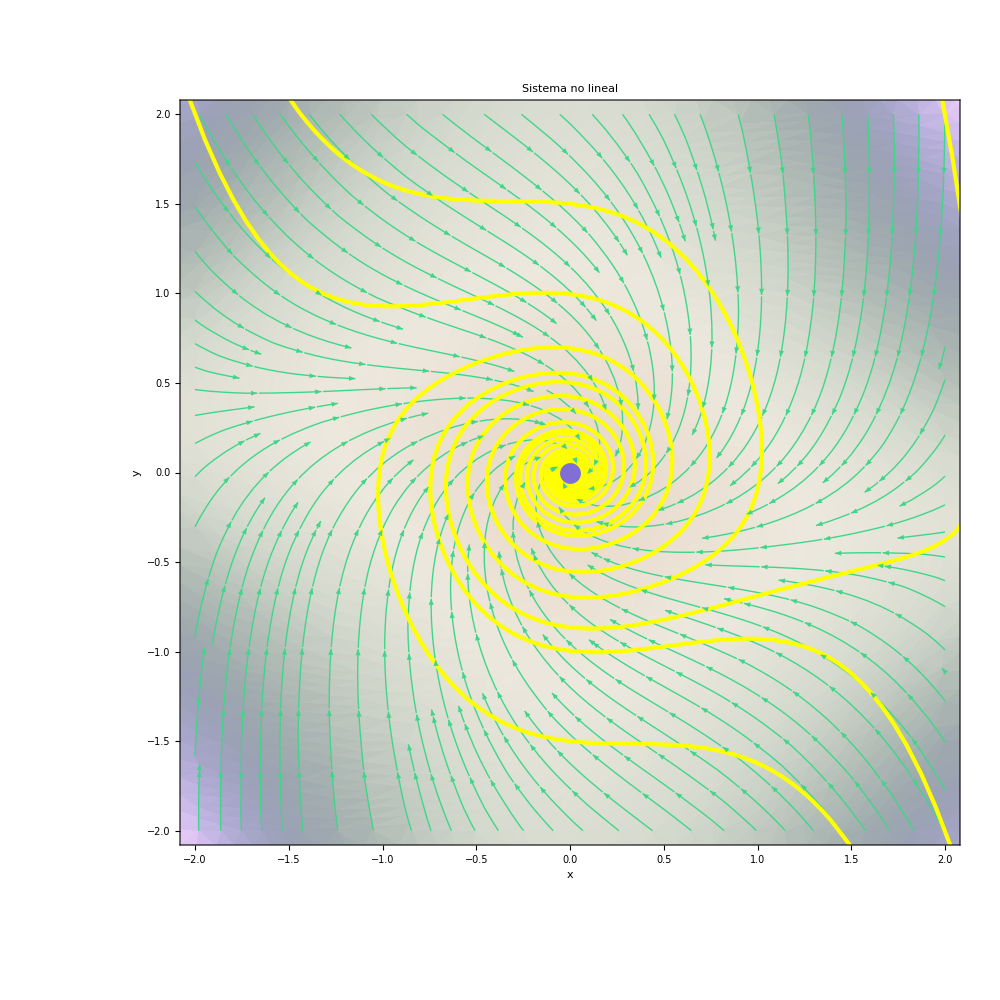

```mathematica
Showing[p31,G1,p11](*Muestra los gráficos*)
```

```mathematica
ClearAll[μ]
```

Caso : μ = 0

```mathematica
μ=0;
```

Calculando las singularidades

```mathematica
K2=SingularidadesR[f2,g2](*Como lo esperabamos solo hay una*)
```

{{x→0,y→0}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM1/.K2[[1]]
```

(0 | 1
-1 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.K2[[1]]//Eigensystem(*Con lo cual es un punto no hiperbolico, como era lo esperado*)
```

{{ⅈ,-ⅈ},{{-ⅈ,1},{ⅈ,1}}}

Observamos que para este caso en coordenadas polares:

```mathematica
fr2[r,θ]//Simplify
```

-r^3 Cos[θ]^2 Sin[θ]^2

Observamos que ṙ=-r^3 Cos[θ]^2 Sin[θ]^2 (≤ 0) lo cual  parece indicar (en conjunto con el retrato de fase) un comportamiento tipo foco estable.

```mathematica
p21=Points[f2,g2];(*Graficando las singularidades*)
```

```mathematica
p41=LinCam[f2,g2,2];(*Graficando Lineas de Corriente*)
```

```mathematica
G2={p[f2,g2,0,1.5,1.5,2500,Yellow,0.002],p[f2,g2,0,1.5,-1.5,26,Yellow,0.002],p[f2,g2,-2,-2,-0.9,26,Yellow,0.002],p[f2,g2,2,2,-0.9,26,Yellow,0.002],p[f2,g2,0,-1.5,-1.5,26,Yellow,0.002]};(*Retrato de fase del sistema considerando 5 curvas solución*)
```

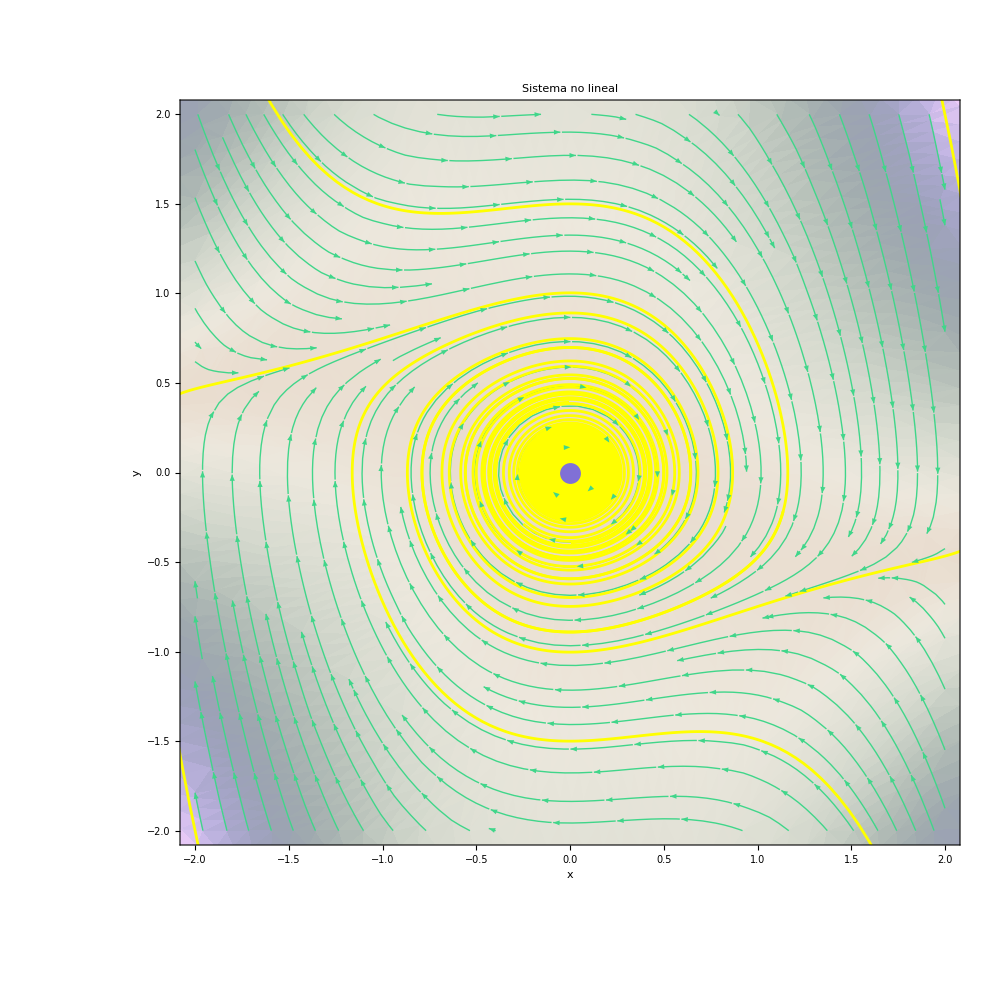

```mathematica
Showing[p41,G2,p21](*Muestra los gráficos*)
```

Observamos que (0,0) es una singularidad tipo foco “débil”

```mathematica
ClearAll[μ]
```

Caso : μ > 0

```mathematica
μ=0.12;
```

Calculando las singularidades

```mathematica
K3=SingularidadesR[f2,g2](*Como lo esperabamos hay 3 valores*)
```

{{x→-2.90746,y→0.348895},{x→0.,y→0},{x→2.90746,y→-0.348895}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM1/.K3[[1]]
```

(0.12 | 1
1.0288 | -8.33333)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.K3[[1]]//Eigensystem(*Con lo cual es una singularidad tipo silla*)
```

{{-8.45333,0.24},{{-0.115855,0.993266},{0.992877,0.119145}}}

Evaluando la matriz Jacobiana en P2:

```mathematica
JM1/.K3[[2]]
```

(0.12 | 1
-1. | 0.12)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.K3[[2]]//Eigensystem(*Con lo cual es una singularidad tipo foco espiral inestable*)
```

{{0.12+1. ⅈ,0.12-1. ⅈ},{{0.707107+0. ⅈ,0.+0.707107 ⅈ},{0.707107+0. ⅈ,0.-0.707107 ⅈ}}}

Evaluando la matriz Jacobiana en P3:

```mathematica
JM1/.K3[[3]]
```

(0.12 | 1
1.0288 | -8.33333)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.K3[[3]]//Eigensystem(*Con lo cual es una singularidad tipo silla*)
```

{{-8.45333,0.24},{{-0.115855,0.993266},{0.992877,0.119145}}}

Graficando:

```mathematica
p71=Points[f2,g2];(*Graficando las singularidades*)
```

```mathematica
p81=LinCam[f2,g2,4];(*Graficando Lineas de Corriente*)
```

```mathematica
G4={p[f2,g2,-3,0,-1,12,RGBColor[0.52,0.18,0.5],0.002],p[f2,g2,3,0,-1.061,11,RGBColor[0.52,0.18,0.5],0.002],p[f2,g2,-2,0,-1.8,11,Orange,0.002],p[f2,g2,2,0,-1.8,11,Orange,0.002],p[f2,g2,0.03,0,-20,200,Yellow,0.002],p[f2,g2,-1.5,1.2,-0.79,10.7,Orange,0.002],p[f2,g2,1.5,-1.2,-0.79,10.7,Orange,0.002],p[f2,g2,3, -2,-0.3,20,RGBColor[0.52,0.18,0.5],0.002],p[f2,g2,-3,2,-0.30,20,RGBColor[0.52,0.18,0.5],0.002]};(*Retrato de fase del sistema considerando 8 curvas solución*)
```

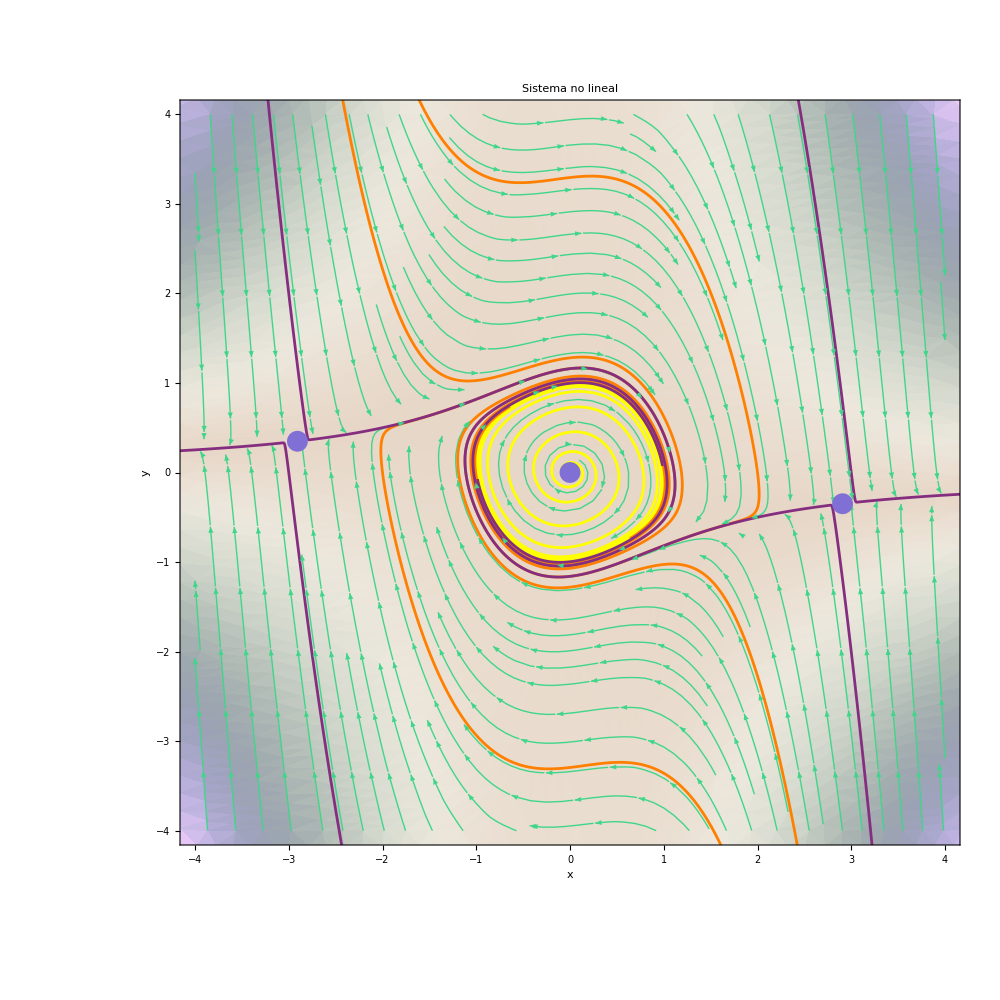

```mathematica
Showing5[p81,G4,p71](*Muestra los gráficos*)
```

Tomando en cuenta la dinámica más cercana a la singularidad (0,0) (las lineas naranjas y amarillas) podemos observar un comportamiento de ciclo límite estable rodeando una singularidad inestable, en este caso un foco espiral inestable.

Por lo que este sistema en parametros cercanos a su valor de bifurcación: μ=0, se comporta como una bifurcación de Hopf Supercrítica, pues observamos un comportamiento estable conforme nos acercamos al valor de bifurcación (foco espiral estable μ<0). En el valor de bifurcación observamos un comportamiento de singularidad (no hiperbólica) debil (de tipo foco estable). Pasando ese valor (μ>0 en valores cercanos a μ=0) podemos observar que cerca a la singularidad en el origen (foco espiral inestable) hay un ciclo límite estable (además hay otras dos singularidades inestables tipo silla a su alrededor).
Como nota me gustaria agregar que si el sistema se aleja mucho de μ>0 el  ciclo límite estable comienza a ser menos evidente o desaparece.

## Pregunta 3

Analizar en forma cualitativa, estableciendo las singularidades, el tipo de bifurcación presente y estructurar el retrato de fase para el sistema:

Sistema:

Piecewise[{{ẋ=, y-2x}, {ẏ=, u+x^2-y}}]

```mathematica
$Assumptions=u∈Reals;
```

```mathematica
f3[x_,y_]:=y-2x
```

```mathematica
g3[x_,y_]:=u+x^2-y
```

```mathematica
P2=Singularidades[f3,g3]
```

{{x→1-√(1-u),y→2 (1-√(1-u))},{x→1+√(1-u),y→2 (1+√(1-u))}}

Observamos que solo hay singularidades tales que u≤1, por lo cual esto nos parece indicar la presencia de un cambio en el comportamiento cualitativo del sistema en este punto.

Matriz Jacobiana:

```mathematica
JM2=JacMatrix[f3,g3]
```

(-2 | 1
2 x | -1)

```mathematica
ClearAll[u]
```

Evaluando la matriz Jacobiana en P1:

```mathematica
JM2/.P2[[1]]
```

(-2 | 1
2 (1-√(1-u)) | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.P2[[1]]//Eigensystem
```

{{1/2 (-3-√(9-8 √(1-u))),1/2 (-3+√(9-8 √(1-u)))},{{-(-1-√(9-8 √(1-u)))/(4 (-1+√(1-u))),1},{-(-1+√(9-8 √(1-u)))/(4 (-1+√(1-u))),1}}}

Evaluando la matriz Jacobiana en P2:

```mathematica
JM2/.P2[[2]]
```

(-2 | 1
2 (1+√(1-u)) | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.P2[[2]]//Eigensystem
```

{{1/2 (-3-√(9+8 √(1-u))),1/2 (-3+√(9+8 √(1-u)))},{{-(1+√(9+8 √(1-u)))/(4 (1+√(1-u))),1},{-(1-√(9+8 √(1-u)))/(4 (1+√(1-u))),1}}}

Caso : u < 1

En este caso he dado 3 valores menores que uno, primero un valor menor que cero, luego u=0 y finalmente un valor entre 0 y 1, solo para ejemplificar el comportamiento silla- nodo en estos tres valores

```mathematica
ClearAll[u]
```

u<0

```mathematica
u=-0.1;
```

```mathematica
L1=P2//N(*Las singularidades son 2*)
```

{{x→-0.0488088,y→-0.0976177},{x→2.04881,y→4.09762}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM2/.L1[[1]]
```

(-2 | 1
-0.0976177 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L1[[1]]//Eigensystem//N
```

{{-1.89036,-1.10964},{{-0.994043,-0.108985},{-0.746863,-0.664978}}}

Vemos que es un nodo estable

Evaluando la matriz Jacobiana en P2:

```mathematica
JM2/.L1[[2]]
```

(-2 | 1
4.09762 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L1[[2]]//Eigensystem//N
```

{{-3.58509,0.585094},{{-0.533569,0.845757},{-0.36078,-0.932651}}}

Vemos que es una singularidad tipo silla

Graficando:

```mathematica
p12=Points[f3,g3];(*Graficando las singularidades*)
```

```mathematica
p32=LinCam3[f3,g3];(*Graficando Lineas de Corriente*)
```

```mathematica
G12={p[f3,g3,3,3,-1.20,5.9,RGBColor[0.9,0.46,0.54]],p[f3,g3,-1,-1,-1,5,RGBColor[0.9,0.46,0.54]],p[f3,g3,1,-1, -1.36,2,RGBColor[0.9,0.46,0.54]],p[f3,g3,-1,1,-1,26,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.8,4, -1.0281771299042217,2.357672988763243,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.8,5,-0.9,6,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.6
,2.6,-1.2,8,RGBColor[0.9,0.46,0.54]],p[f3,g3,0
,3,-1.2,8,RGBColor[0.9,0.46,0.54]],p[f3,g3,3
,0,-1.,8,RGBColor[0.9,0.46,0.54]]};(*Retrato de fase del sistema considerando 9 curvas solución*)
```

```mathematica
Showing3[p32,G12,p12](*Muestra los gráficos*)
```

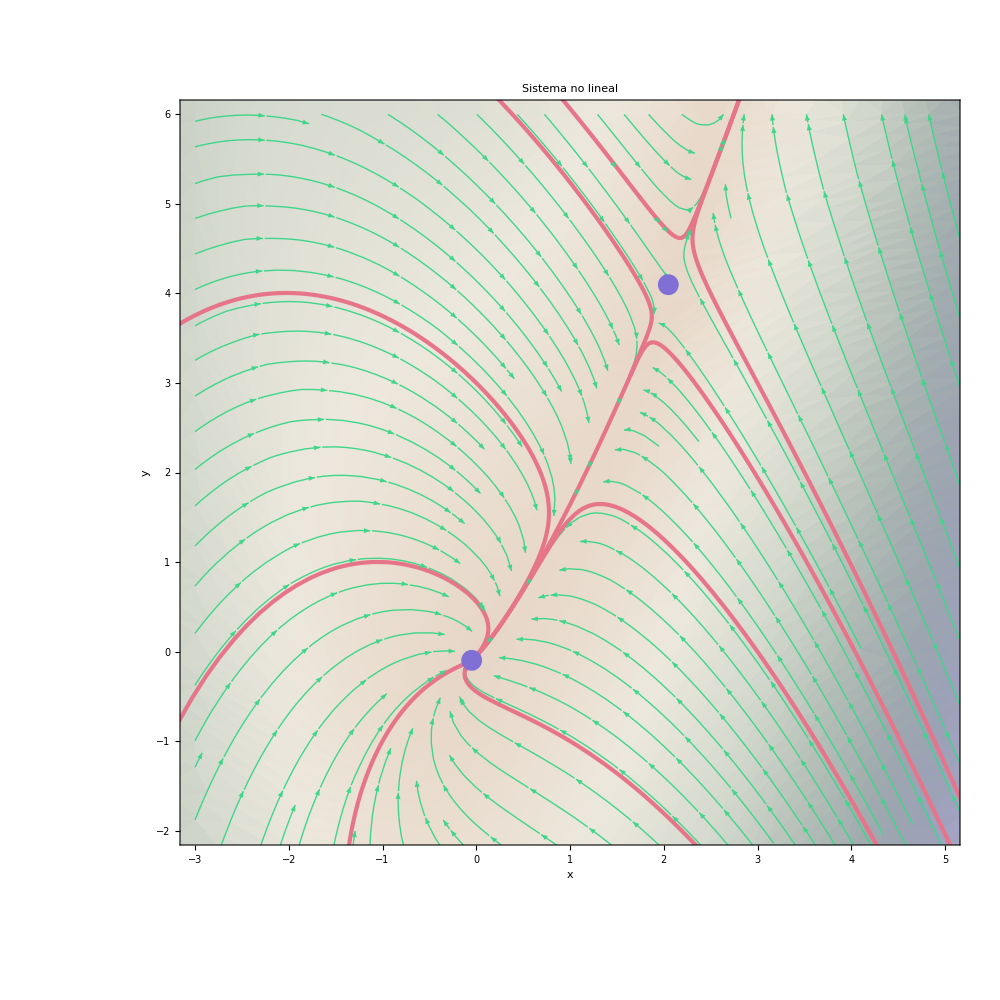

```mathematica
ClearAll[u]
```

u=0

```mathematica
u=0;
```

```mathematica
L2=P2(*Las singularidades son 2*)
```

{{x→0,y→0},{x→2,y→4}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM2/.L2[[1]]
```

(-2 | 1
0 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L2[[1]]//Eigensystem//N
```

{{-2.,-1.},{{1.,0.},{1.,1.}}}

Vemos que es un nodo estable

Evaluando la matriz Jacobiana en P2:

```mathematica
JM2/.L2[[2]]
```

(-2 | 1
4 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L2[[2]]//Eigensystem//N
```

{{-3.56155,0.561553},{{-0.640388,1.},{0.390388,1.}}}

Vemos que es una singularidad tipo silla

Graficando:

```mathematica
p22=Points[f3,g3];(*Graficando las singularidades*)
```

```mathematica
p42=LinCam3[f3,g3];(*Graficando Lineas de Corriente*)
```

```mathematica
G22={p[f3,g3,-1,1.2,-1.20,5.65,RGBColor[0.9,0.46,0.54]],p[f3,g3,-1,-1,-1,5,RGBColor[0.9,0.46,0.54]],p[f3,g3,1,-1, -1.3663913511283348,2.5,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.5,3,-1.2,12,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.5,3.8, -1.0281771299042217,2.357672988763243,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.8,5,-0.9, 5.7776218747,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.2,5,-1,4.705391070744530,RGBColor[0.9,0.46,0.54]],p[f3,g3,0
,3,-1.2,8,RGBColor[0.9,0.46,0.54]],p[f3,g3,3
,0,-1.,8,RGBColor[0.9,0.46,0.54]]};(*Retrato de fase del sistema considerando 9 curvas solución*)
```

```mathematica
Showing3[p42,G22,p22](*Muestra los gráficos*)
```

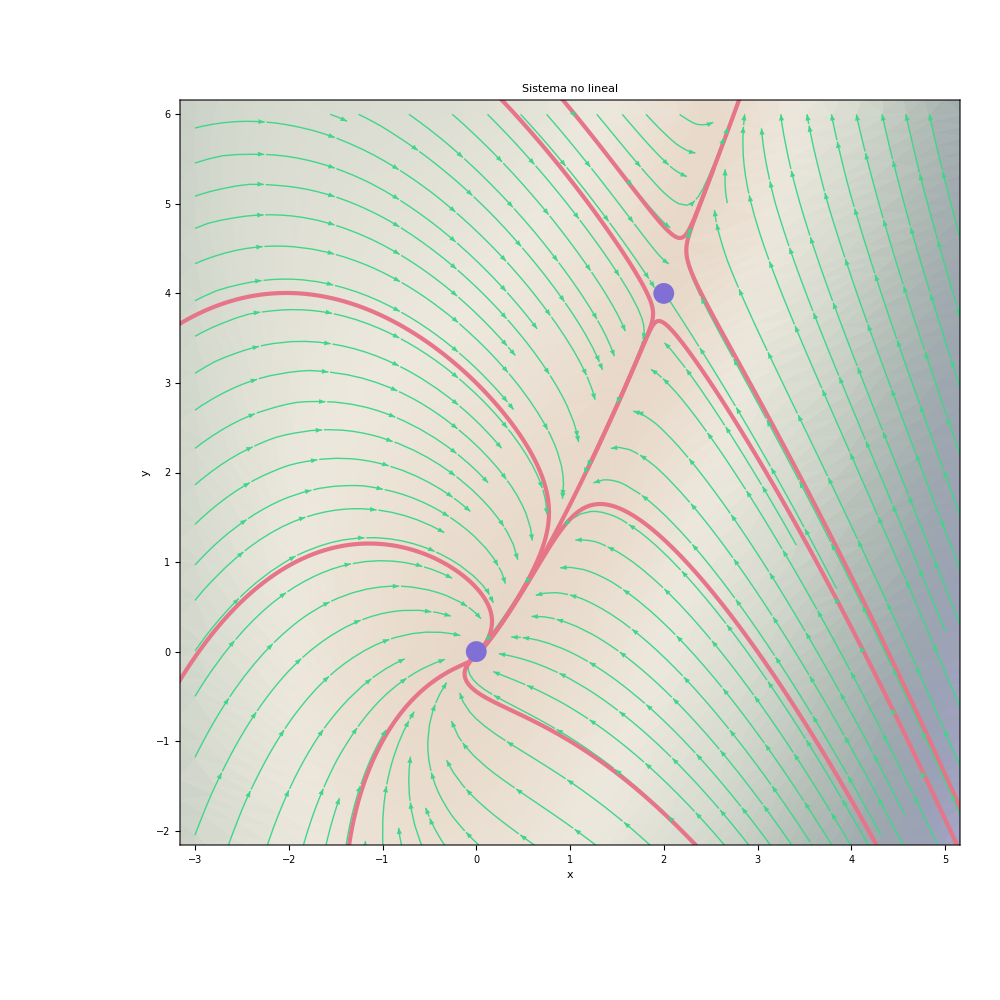

```mathematica
ClearAll[u]
```

0<u<1

```mathematica
u=0.5;
```

```mathematica
L3=P2(*Las singularidades son 2*)
```

{{x→0.292893,y→0.585786},{x→1.70711,y→3.41421}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM2/.L3[[1]]
```

(-2 | 1
0.585786 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L3[[1]]//Eigensystem//N
```

{{-2.41421,-0.585786},{{-0.92388,0.382683},{-0.57735,-0.816497}}}

Vemos que es un nodo estable

Evaluando la matriz Jacobiana en P2:

```mathematica
JM2/.L3[[2]]
```

(-2 | 1
3.41421 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L3[[2]]//Eigensystem//N
```

{{-3.41421,0.414214},{{-0.57735,0.816497},{-0.382683,-0.92388}}}

Vemos que es una singularidad tipo silla

Observamos que la dinamica de las singularidades no ha variado hasta este punto, siendo una singularidad estable (nodo estable) y una inestable(ensilladura) para todos los casos (cercanos a 1, en valores menores se pueden encontrar pares focos espirales estables-sillas), lo cual nos lleva a pensar que probablemente halla una bifurcación en u=1 (valor de bifurcación) y que esta sea una bifurcación tipo silla-nodo ya que no hay ninguna singularidad cuando u>1.

Graficando:

```mathematica
p52=Points[f3,g3];(*Graficando las singularidades*)
```

```mathematica
p72=LinCam3[f3,g3];(*Graficando Lineas de Corriente*)
```

```mathematica
G32={p[f3,g3,-1.8,0.5,-1.20,5.65,RGBColor[0.9,0.46,0.54]],p[f3,g3,-1,-1,-1,5,RGBColor[0.9,0.46,0.54]],p[f3,g3,1,-1, - 1.3546882686448507,2.5,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.3,3,-1.2,6.22517752018,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.5,2, -1.0281771299042217,15,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.2,3.8,-0.9, 5.7776218747,RGBColor[0.9,0.46,0.54]],p[f3,g3,0.8,5,-1,4.705391070744530,RGBColor[0.9,0.46,0.54]],p[f3,g3,0.8
,1.8,-2,8,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.3
,0,-1.,8,RGBColor[0.9,0.46,0.54]]};(*Retrato de fase del sistema considerando 9 curvas solución*)
```

```mathematica
Showing3[p72,G32,p52](*Muestra los gráficos*)
```

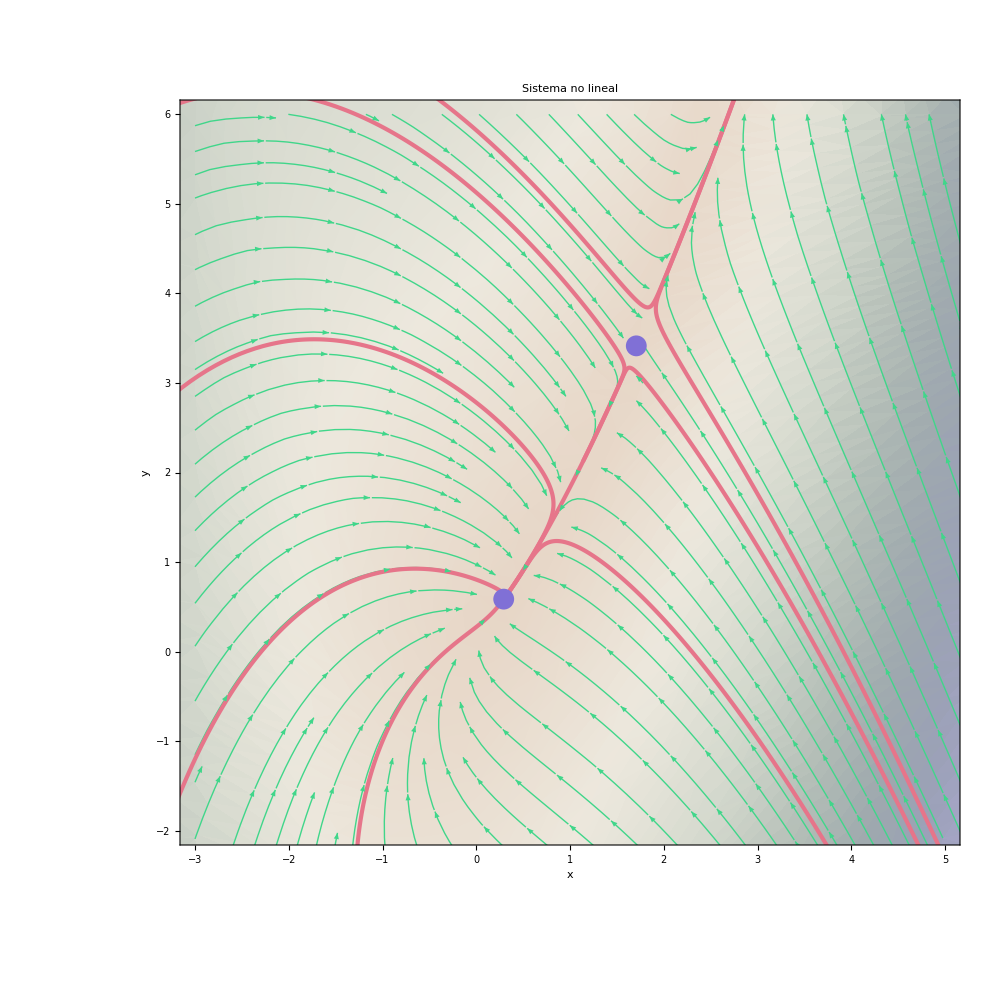

```mathematica
ClearAll[u]
```

Caso: u=1

```mathematica
u=1;
```

```mathematica
L4=SingularidadesR[f3,g3](*Solo hay una singularidad*)
```

{{x→1,y→2}}

Evaluando la matriz Jacobiana en P1:

```mathematica
JM2/.L4[[1]]
```

(-2 | 1
2 | -1)

Obteniendo los autovalores:

```mathematica
Jac[f3,g3]/.L4[[1]]//Eigensystem//N
```

{{-3.,0.},{{-1.,1.},{1.,2.}}}

Vemos que es una singularidad no hiperbolica

Graficando:

```mathematica
p82=Points[f3,g3];(*Graficando las singularidades*)
```

```mathematica
p92=LinCam3[f3,g3];(*Graficando Lineas de Corriente*)
```

```mathematica
G42={p[f3,g3,1,3,-2,12,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.5,2.5,-1.2,5,RGBColor[0.9,0.46,0.54]],p[f3,g3,-1,-1,-2,180,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.4,2.6, -1.0281771299042217,6.7933140010,RGBColor[0.9,0.46,0.54]],p[f3,g3,0.8,5,-1,4.705391070744530,RGBColor[0.9,0.46,0.54]],p[f3,g3,0,1,-2,12,RGBColor[0.9,0.46,0.54]],p[f3,g3,0.5,2.5,-1,12,RGBColor[0.9,0.46,0.54]],p[f3,g3,0,1,-1,12,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.1,1.96,-2,50,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.3,0,-1.343610545314033,2.5,RGBColor[0.9,0.46,0.54]]};(*Retrato de fase del sistema considerando 9 curvas solución*)
```

```mathematica
Showing4[p92,G42,p82](*Muestra los gráficos*)
```

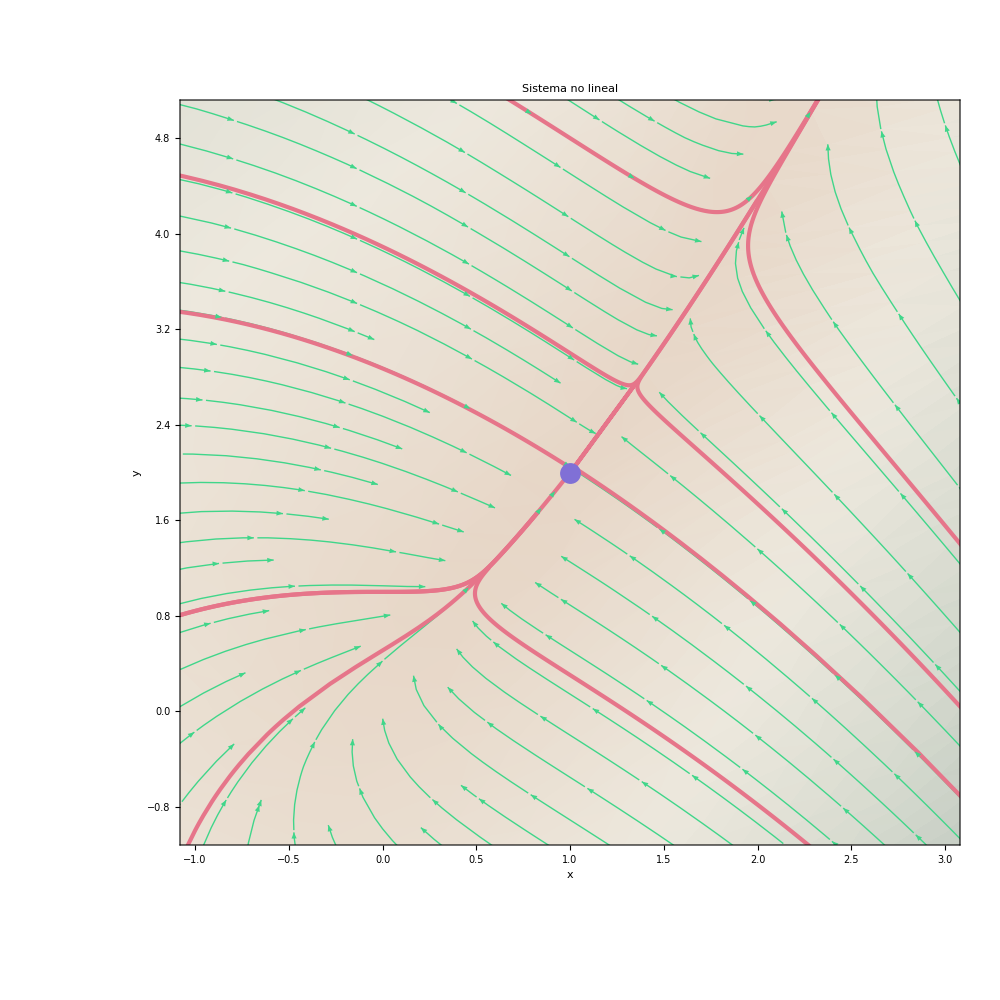

```mathematica
ClearAll[u]
```

Caso: u>1

```mathematica
u=1.5;
```

```mathematica
L4=SingularidadesR[f3,g3](*No hay singularidades, como era esperado*)
```

{}

Graficando:

```mathematica
p112=LinCam3[f3,g3];(*Graficando Lineas de Corriente*)
```

```mathematica
G52={p[f3,g3,1,3,-2,5.68997151243,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.5,2.5,-1.6705569833,5.5,RGBColor[0.9,0.46,0.54]],p[f3,g3,0,0,-1.9,8.7,RGBColor[0.9,0.46,0.54]],p[f3,g3,2.5,2, -1.0281771299042217,4.6,RGBColor[0.9,0.46,0.54]],p[f3,g3,0.8,5,-2,4.4,RGBColor[0.9,0.46,0.54]],p[f3,g3,0,1,-2,8,RGBColor[0.9,0.46,0.54]],p[f3,g3,0.5,2.5,-1,6.5,RGBColor[0.9,0.46,0.54]],p[f3,g3,0,2,-1,7.4,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.1,1.96,-1.8,6,RGBColor[0.9,0.46,0.54]],p[f3,g3,1.3,0,-1.34,2.5,RGBColor[0.9,0.46,0.54]]};(*Retrato de fase del sistema considerando 8 curvas solución*)
```

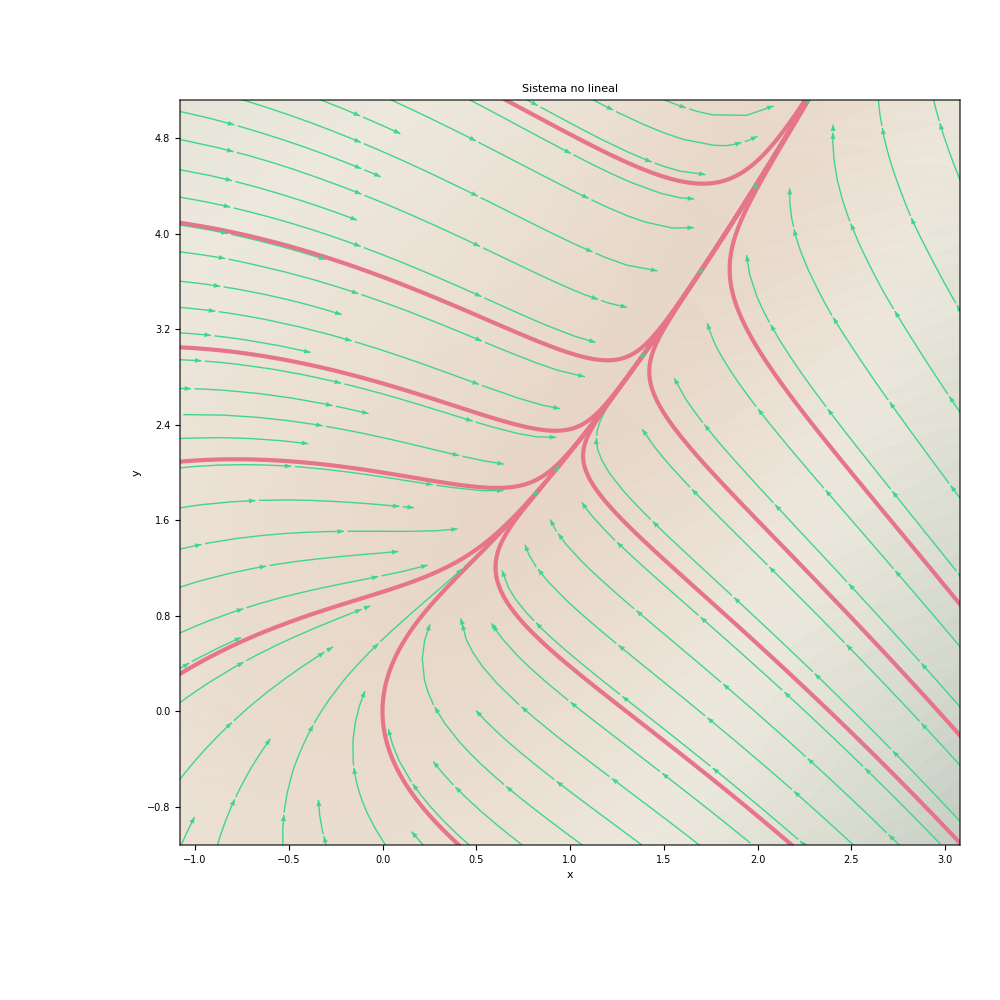

```mathematica
Showing4[p112,G52](*Muestra los gráficos*)
```

Todo lo visto hasta este momento inidica que es una bifurcación tipo silla-nodo, con un valor de bifurcación u=1.
Primero en valores u<1 hemos encontrado la presencia de dos singularidades, una ensilladura y un nodo, luego en el valor de bifurcación u=1 encontramos una singularidad no hiperbolica y finalemente en u>1 no encontramos ninguna singularidad.